## Initialization Block

```mathematica
SetDirectory[NotebookDirectory[]];
β:=1/(k T);
βe:=1/(k Te);
Off[NIntegrate::inumr]
Off[NIntegrate::slwcon]
Off[NIntegrate::ncvb]

(*A/electric spectral function*)
A1[ϵ_,t_]:=(2((ϵ-ϵ2)^2+t^2+γ2^2)γ1)/(((ϵ-ϵ1+ⅈ γ1)(ϵ-ϵ2+ⅈ γ2)-t^2) ((ϵ-ϵ1-ⅈ γ1)(ϵ-ϵ2-ⅈ γ2)-t^2))
A2[ϵ_,t_]:=(2((ϵ-ϵ1)^2+t^2+γ1^2)γ2)/(((ϵ-ϵ1+ⅈ γ1)(ϵ-ϵ2+ⅈ γ2)-t^2) ((ϵ-ϵ1-ⅈ γ1)(ϵ-ϵ2-ⅈ γ2)-t^2))

(*Aph/phonon spectral function*)
Aph[ω_]:=(4 γph ω)/(((ω+I γph)^2-Ω^2)((ω-I γph)^2-Ω^2));

(*n/distribution*)
nb[ϵ_,T_]:=1/(ⅇ^(ϵ/(k T))-1)
nf[ϵ_,T_]:=1/(ⅇ^(ϵ/(k T))+1)
(*Λ/DOS in m^2*)
Λ11[ω_]:=-1/(2 π)NIntegrate[((4 t^2 γ1^2 (-2 ϵ+2 ϵ2+ℏ ω)^2)/((t^2+(ⅈ γ1-ϵ+ϵ1) (-ⅈ γ2+ϵ-ϵ2)) (t^2+(-ⅈ γ1-ϵ+ϵ1) (ⅈ γ2+ϵ-ϵ2)) (t^2+(ⅈ γ1+ϵ-ϵ1-ℏ ω) (-ⅈ γ2-ϵ+ϵ2+ℏ ω)) (t^2+(-ⅈ γ1+ϵ-ϵ1-ℏ ω) (ⅈ γ2-ϵ+ϵ2+ℏ ω))))(1/(ⅇ^(βe(ϵ-μ1))+1)-1/(ⅇ^(βe(ϵ-μ1-ℏ ω))+1)),{ϵ,0,∞}];
Λ12[ω_]:=-1/(2 π)NIntegrate[((4 γ1 γ2 (t^4+2 t^2 (γ1 γ2+(ϵ-ϵ2) (ϵ-ϵ1-ℏ ω))+(γ2^2+(ϵ-ϵ2)^2) (γ1^2+(-ϵ+ϵ1+ℏ ω)^2)))/((t^2+(ⅈ γ1-ϵ+ϵ1) (-ⅈ γ2+ϵ-ϵ2)) (t^2+(-ⅈ γ1-ϵ+ϵ1) (ⅈ γ2+ϵ-ϵ2)) (t^2+(ⅈ γ1+ϵ-ϵ1-ℏ ω) (-ⅈ γ2-ϵ+ϵ2+ℏ ω)) (t^2+(-ⅈ γ1+ϵ-ϵ1-ℏ ω) (ⅈ γ2-ϵ+ϵ2+ℏ ω))))(1/(ⅇ^(βe(ϵ-μ1))+1)-1/(ⅇ^(βe(ϵ-μ2-ℏ ω))+1)),{ϵ,0,∞}];
Λ21[ω_]:=-1/(2 π)NIntegrate[((4 γ1 γ2 (t^4+2 t^2 (γ1 γ2+(ϵ-ϵ1) (ϵ-ϵ2-ℏ ω))+(γ1^2+(ϵ-ϵ1)^2) (γ2^2+(-ϵ+ϵ2+ℏ ω)^2)))/((t^2+(ⅈ γ1-ϵ+ϵ1) (-ⅈ γ2+ϵ-ϵ2)) (t^2+(-ⅈ γ1-ϵ+ϵ1) (ⅈ γ2+ϵ-ϵ2)) (t^2+(ⅈ γ1+ϵ-ϵ1-ℏ ω) (-ⅈ γ2-ϵ+ϵ2+ℏ ω)) (t^2+(-ⅈ γ1+ϵ-ϵ1-ℏ ω) (ⅈ γ2-ϵ+ϵ2+ℏ ω))))(1/(ⅇ^(βe(ϵ-μ2))+1)-1/(ⅇ^(βe(ϵ-μ1-ℏ ω))+1)),{ϵ,0,∞}];
Λ22[ω_]:=-1/(2 π)NIntegrate[((4 t^2 γ2^2 (-2 ϵ+2 ϵ1+ℏ ω)^2)/((t^2+(ⅈ γ1-ϵ+ϵ1) (-ⅈ γ2+ϵ-ϵ2)) (t^2+(-ⅈ γ1-ϵ+ϵ1) (ⅈ γ2+ϵ-ϵ2)) (t^2+(ⅈ γ1+ϵ-ϵ1-ℏ ω) (-ⅈ γ2-ϵ+ϵ2+ℏ ω)) (t^2+(-ⅈ γ1+ϵ-ϵ1-ℏ ω) (ⅈ γ2-ϵ+ϵ2+ℏ ω))))(1/(ⅇ^(βe(ϵ-μ2))+1)-1/(ⅇ^(βe(ϵ-μ2-ℏ ω))+1)),{ϵ,0,∞}];


(*T/Transmission rate*)
T11[ω_]:=Re[Λ11[ω]*Aph[ω]];
T12[ω_]:=Re[Λ12[ω]*Aph[ω]];
T21[ω_]:=Re[Λ21[ω]*Aph[ω]];
T22[ω_]:=Re[Λ22[ω]*Aph[ω]];
(*J/Heat flux*)
J11:=2NIntegrate[ℏ ω T11[ω](1/(ⅇ^(βe(ℏ ω-(μ1-μ1)))-1)-1/(ⅇ^(β ℏ ω)-1)),{ω,0,∞}]
J12:=2NIntegrate[ℏ ω T12[ω](1/(ⅇ^(βe(ℏ ω-(μ1-μ2)))-1)-1/(ⅇ^(β ℏ ω)-1)),{ω,0,∞}]
J21:=2NIntegrate[ℏ ω T21[ω](1/(ⅇ^(βe(ℏ ω-(μ2-μ1)))-1)-1/(ⅇ^(β ℏ ω)-1)),{ω,0,∞}]
J22:=2NIntegrate[ℏ ω T22[ω](1/(ⅇ^(βe(ℏ ω-(μ2-μ2)))-1)-1/(ⅇ^(β ℏ ω)-1)),{ω,0,∞}]
(*Je/Electronic current in e*)
Je12:=2NIntegrate[- T12[ω](1/(ⅇ^(βe(ℏ ω-(μ1-μ2)))-1)-1/(ⅇ^(β ℏ ω)-1)),{ω,0,∞}]
Je21:=2NIntegrate[ T21[ω](1/(ⅇ^(βe(ℏ ω-(μ2-μ1)))-1)-1/(ⅇ^(β ℏ ω)-1)),{ω,0,∞}]
(*DOS spectrum grid*)
p1:=Plot[{ Λ11[ω],Λ12[ω], Λ21[ω],Λ22[ω]},{ω,-3,3},PlotLegends->"Expressions",AxesLabel->{"ω"," Λ(ω)"}]
p2:=Plot[{T11[ω],T12[ω],T21[ω],T22[ω]},{ω,-3,3},PlotLegends->"Expressions",AxesLabel->{"ω","T(ω)"}]
p3:=ParametricPlot[{{6-nf[ϵ-μ2,Te],ϵ},
{4-A2[ϵ,t]/4,ϵ},
{2+A1[ϵ,t]/4,ϵ},
{nf[ϵ-μ1,Te],ϵ}},
{ϵ,0,20},PlotRange->{{0,6},{0,20}},Frame->True,FrameTicks->{{All,None},{None,None}},PlotLegends->{"n_F(ϵ-μ2)","A2","A1","n_F(ϵ-μ1)"},AspectRatio->1]
p4:=Plot[ω T12[ω](1/(ⅇ^(βe(ℏ ω-(μ1-μ2)))-1)-1/(ⅇ^(β ℏ ω)-1))+ω T21[ω](1/(ⅇ^(βe(ℏ ω-(μ2-μ1)))-1)-1/(ⅇ^(β ℏ ω)-1))+ω T11[ω](1/(ⅇ^(βe(ℏ ω-(μ1-μ1)))-1)-1/(ⅇ^(β ℏ ω)-1))+ω T22[ω](1/(ⅇ^(βe(ℏ ω-(μ2-μ2)))-1)-1/(ⅇ^(β ℏ ω)-1)),{ω,-3,3},PlotLegends->"Expressions",AxesLabel->{"ω","j(ω)"}]

p000:=Plot[{1/(ⅇ^(β(ℏ ω-(μ1-μ2)))-1),1/(ⅇ^(β(ℏ ω-(μ2-μ1)))-1),1/(ⅇ^(β ℏ ω)-1)},{ω,-3,3},PlotLegends->"Expressions",AxesLabel->{"ω","n_B(ω-μ_ij)"}]

SPG:=Grid [{{p1,p2},{p3,p4}},Frame->All]
```

## Operation 0: Systematic Checking

### Hopping Term Check

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

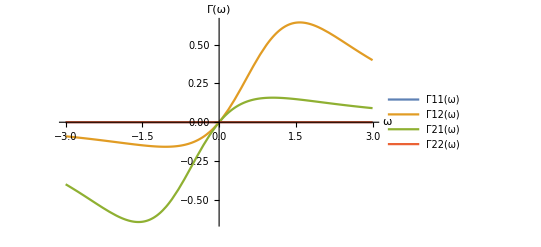
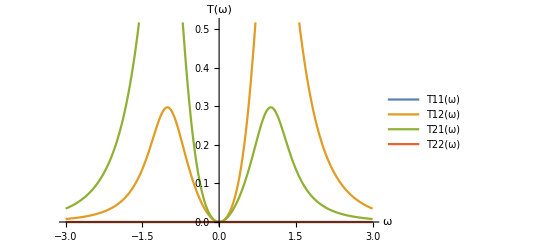
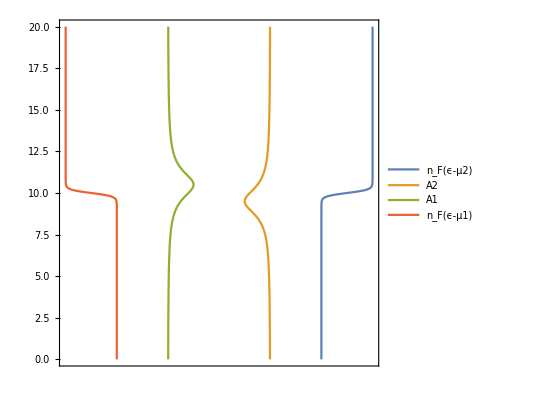
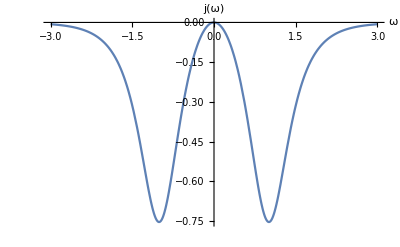
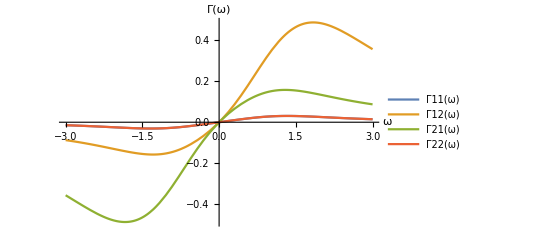
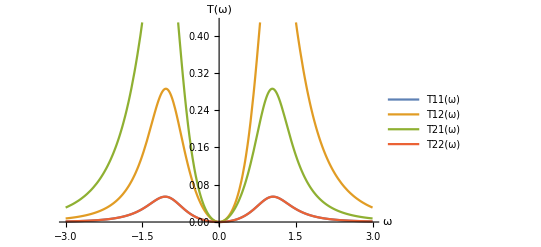
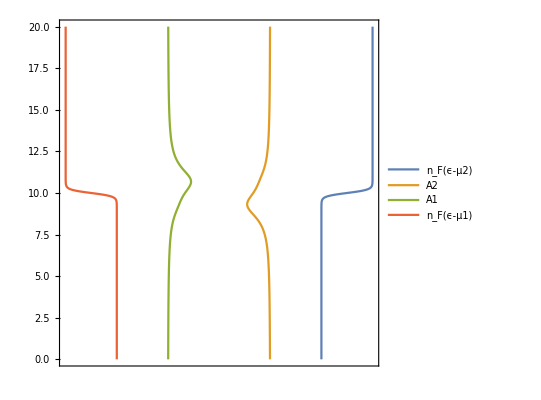
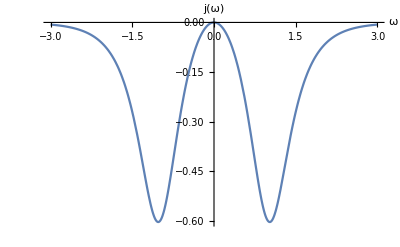
{-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-}

```mathematica
{
ℏ=1,Ω=1,k=1,T=1,Te=0.1,
γ1=1,γ2=1,
μ1=10,μ2=10,
ϵ1=10.5,ϵ2=9.5,t=0,
γph=0.5
};
plots=Table[SPG,{t,0,2,0.5}]
ListAnimate[plots]
```

### Hopping Adjustment

Now hopping term is not zero but with t12, set the magnitude of t12 to be t. And see what will the electron energy spectrum change.

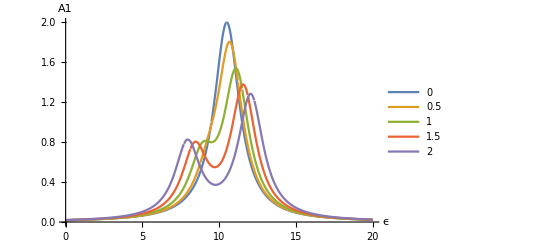

```mathematica
{
ℏ=1,k=1,T=1,Te=1,
Ω=1,
γ1=1,γ2=1,
μ1=9.5,μ2=10.5,
ϵ1=10.5,ϵ2=9.5,t=0,
γph=0.5
};
Plot[{A1[ϵ,0],A1[ϵ,0.5],A1[ϵ,1],A1[ϵ,1.5],A1[ϵ,2]},{ϵ,0,20},PlotRange->{0,2},PlotLegends->{0,0.5,1,1.5,2},AxesLabel->{"ϵ","A1"}]
```

We can prove it when t = 0,

A_1=(2((ϵ-ϵ2)^2+t^2+γ2^2)γ1)/(((ϵ-ϵ1+ⅈ γ1)(ϵ-ϵ2+ⅈ γ2)-t^2) ((ϵ-ϵ1-ⅈ γ1)(ϵ-ϵ2-ⅈ γ2)-t^2))
=(2((ϵ-ϵ2)^2+γ2^2)γ1)/((ϵ-ϵ1+ⅈ γ1)(ϵ-ϵ2+ⅈ γ2))(ϵ-ϵ1-ⅈ γ1)(ϵ-ϵ2-ⅈ γ2))
=(2 γ1)/((ϵ-ϵ1)^2+γ1^2)

the right side backs to none-hopping energy spectrum.

### System Diagram

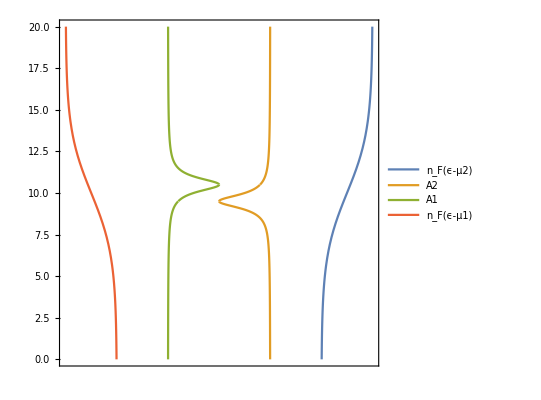

```mathematica
{
ℏ=1,Ω=1,k=1,T=1,Te=1.9,
γ1=0.5,γ2=0.5,
μ1=10,μ2=10,
ϵ1=10.5,ϵ2=9.5,t=0,
γph=0.5
};
p4
```

### Heat Flux Spectrum Check

j(ω) should be symmetric about 0.

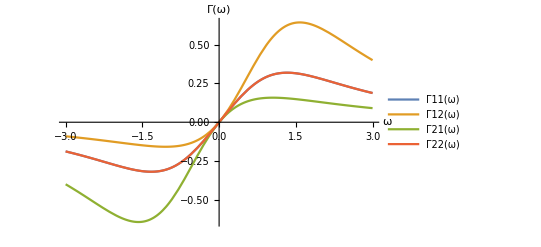
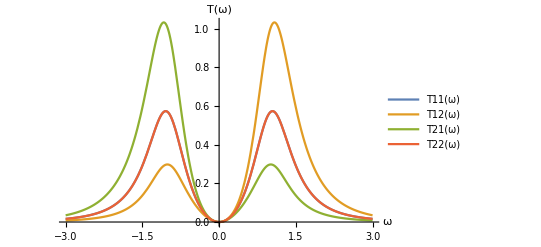
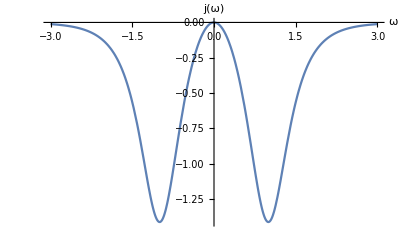
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{
ℏ=1,Ω=1,k=1,T=1,Te=0.1,
γ1=1,γ2=1,
μ1=10,μ2=10,
ϵ1=10.5,ϵ2=9.5,t=0,
γph=0.5
};
SPG
```

## Operation 1: Heat Rectification

### J-ΔT in different μ

Change ΔT = Te - Tph, μ=μ1=μ2, keep the other parameters.

```mathematica
{
ℏ=1,Ω=1,k=1,T=1,Te=0.1,
γ1=0.5,γ2=0.5,
μ1=10,μ2=10,
ϵ1=10.5,ϵ2=9.5,t=0,
γph=0.5
};

datas=Table[μ1=μ;μ2=μ;Te=T+ΔT;{ΔT,J11+J12+J21+J22},{μ,10,16},{ΔT,-0.9,0.9,0.1}]
Export["op1.J.json",datas]
```

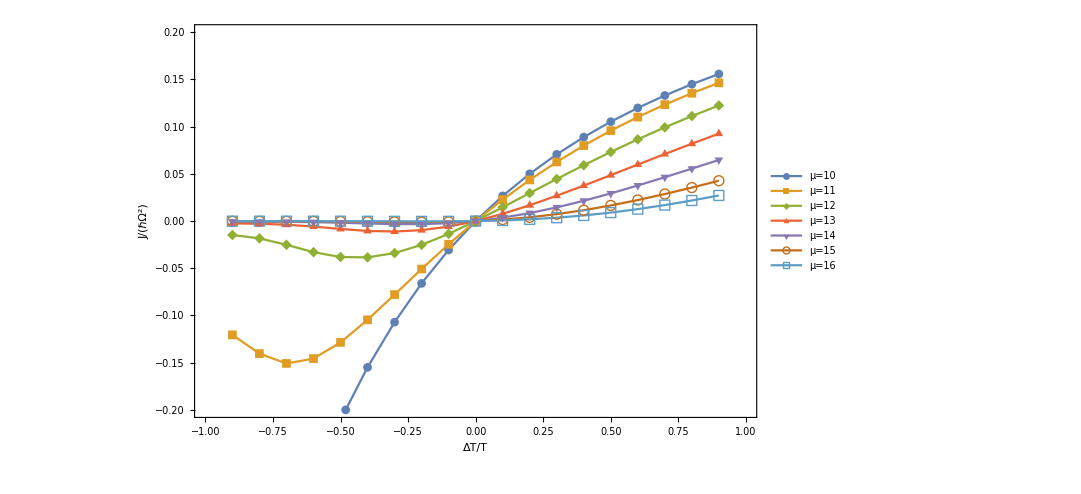

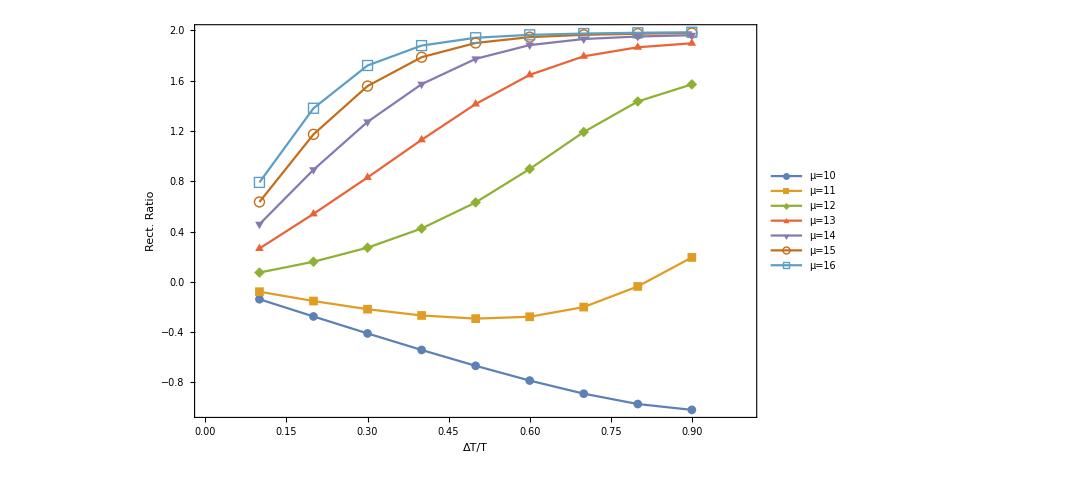

```mathematica
datas=Import["op1.J.json"];
styles={
LabelStyle->Directive[Black,16,FontFamily->"Times"],
TicksStyle->Directive[Black,24,Thick,FontFamily->"Times"],
FrameStyle->Directive[Black,24,Thick,FontFamily->"Times"]};

(*Rescale unit*)
datas⟦All,All,2⟧=datas⟦All,All,2⟧/(2π);
datasRR=Table[{1-0.1i,2(#⟦-i,2⟧+#⟦i,2⟧)/(#⟦-i,2⟧-#⟦i,2⟧)},{i,(Length[datas[[1]]]-1)/2}]&/@datas;
ListLinePlot[datas,PlotRange->{{-1.0,1.0},{-0.2,0.2}},
FrameLabel->{"ΔT/T","J/(ℏΩ^2)"},
PlotLegends->Placed[{"μ=10","μ=11","μ=12","μ=13","μ=14","μ=15","μ=16"},{0.7,0.3}],
styles,
PlotMarkers->Automatic,
Frame->True,FrameStyle->Directive[Black,Thick],
ImageSize->800
]
ListLinePlot[datasRR,PlotRange->{{0.0,1.0},All},
FrameLabel->{"ΔT/T","Rect. Ratio"},
PlotLegends->Placed[{"μ=10","μ=11","μ=12","μ=13","μ=14","μ=15","μ=16"},{0.7,0.45}],
styles,
Frame->True,
PlotMarkers->Automatic,
ImageSize->800
]
```

Curves of μ = 7 and 13 are extremely close.

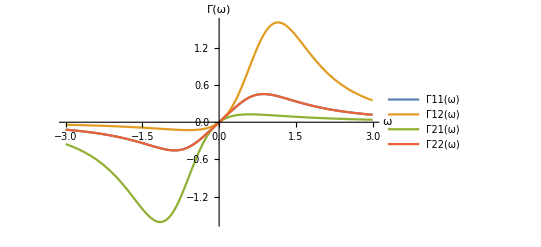
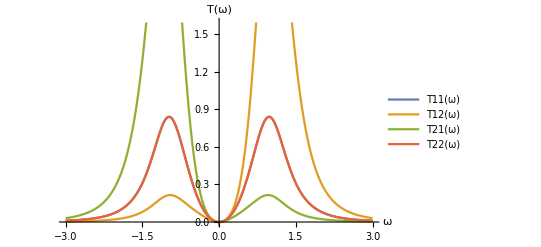
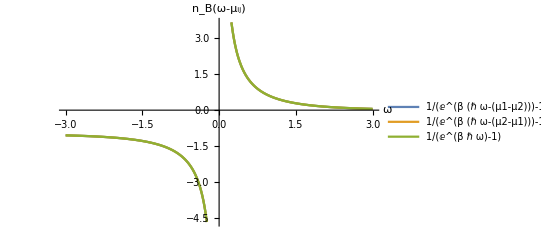
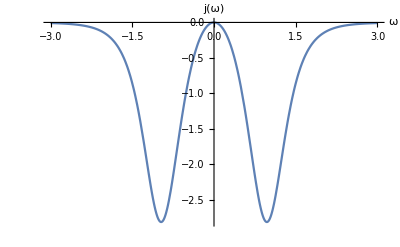
-Graphics- | -Graphics-
-Graphics- | -Graphics-

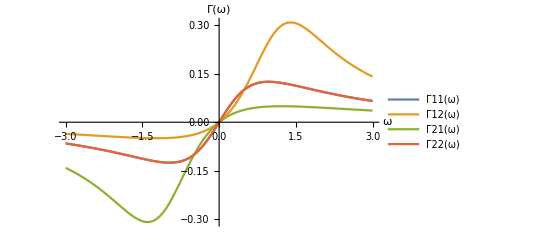
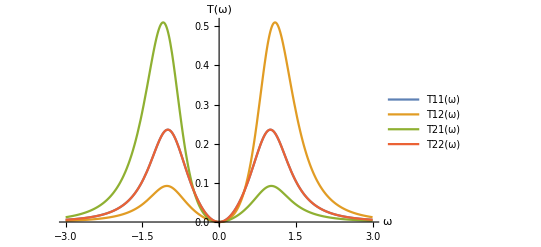
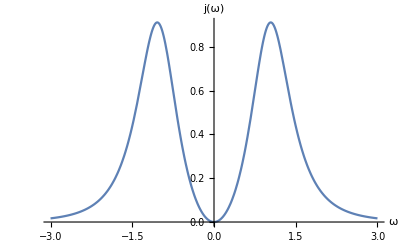
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{
ℏ=1,Ω=1,k=1,T=1,Te=0.1,
γ1=0.5,γ2=0.5,
μ1=10,μ2=10,
ϵ1=10.5,ϵ2=9.5,t=0,
γph=0.5
};
SPG
Te=1.9;
SPG
```

### J-ΔT in different γ

Change ΔT = Te - Tph, γ = γ1 = γ2, keep the other parameters.

```mathematica
data1={};
γ1=1;γ2=1;
For[ΔT=-0.9,ΔT≤0.9,ΔT=ΔT+0.1,
PrintTemporary["Current para:"~~ToString[ΔT]];
Te=T+ΔT;
data1=data1~AppendTo~{ΔT,J11+J12+J21+J22}
]
data2={};
γ1=2;γ2=2;
For[ΔT=-0.9,ΔT≤0.9,ΔT=ΔT+0.1,
PrintTemporary["Current para:"~~ToString[ΔT]];
Te=T+ΔT;
data2=data2~AppendTo~{ΔT,J11+J12+J21+J22}
]
data3={};
γ1=4;γ2=4;
For[ΔT=-0.9,ΔT≤0.9,ΔT=ΔT+0.1,
PrintTemporary["Current para:"~~ToString[ΔT]];
Te=T+ΔT;
data3=data3~AppendTo~{ΔT,J11+J12+J21+J22}
]
data4={};
γ1=32;γ2=32;
For[ΔT=-0.9,ΔT≤0.9,ΔT=ΔT+0.1,
PrintTemporary["Current para:"~~ToString[ΔT]];
Te=T+ΔT;
data4=data4~AppendTo~{ΔT,J11+J12+J21+J22}
]


dr1={};dr2={};dr3={};dr4={};
For[i=1,i≤9,i++,
dr1=dr1~AppendTo~{1-0.1i,2(data1⟦-i,2⟧+data1⟦i,2⟧)/(data1⟦-i,2⟧-data1⟦i,2⟧)};
dr2=dr2~AppendTo~{1-0.1i,2(data2⟦-i,2⟧+data2⟦i,2⟧)/(data2⟦-i,2⟧-data2⟦i,2⟧)};
dr3=dr3~AppendTo~{1-0.1i,2(data3⟦-i,2⟧+data3⟦i,2⟧)/(data3⟦-i,2⟧-data3⟦i,2⟧)};
dr4=dr4~AppendTo~{1-0.1i,2(data4⟦-i,2⟧+data4⟦i,2⟧)/(data4⟦-i,2⟧-data4⟦i,2⟧)};
]

ListLinePlot[{data1,data2,data3,data4},AxesLabel->{"ΔT","J"},Frame->True,{"γ=1","γ=2","γ=4","γ=32"},PlotMarkers->Automatic]
ListLinePlot[{dr1,dr2,dr3,dr4},AxesLabel->{"ΔT","R"},Frame->True,PlotLegends->{"γ=1","γ=2","γ=4","γ=32"},PlotLabel->"Heat Rectification Rate",PlotMarkers->Automatic]
```

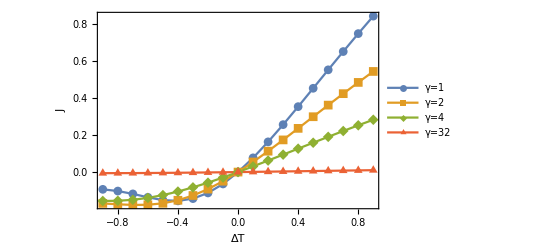

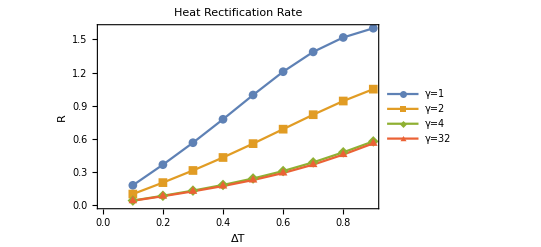

```mathematica
dr1={};dr2={};dr3={};dr4={};
For[i=1,i≤9,i++,
dr1=dr1~AppendTo~{1-0.1i,2(data1⟦-i,2⟧+data1⟦i,2⟧)/(data1⟦-i,2⟧-data1⟦i,2⟧)};
dr2=dr2~AppendTo~{1-0.1i,2(data2⟦-i,2⟧+data2⟦i,2⟧)/(data2⟦-i,2⟧-data2⟦i,2⟧)};
dr3=dr3~AppendTo~{1-0.1i,2(data3⟦-i,2⟧+data3⟦i,2⟧)/(data3⟦-i,2⟧-data3⟦i,2⟧)};
dr4=dr4~AppendTo~{1-0.1i,2(data4⟦-i,2⟧+data4⟦i,2⟧)/(data4⟦-i,2⟧-data4⟦i,2⟧)};
]

ListLinePlot[{data1,data2,data3,data4},AxesLabel->{"ΔT","J"},Frame->True,PlotLegends->{"γ=1","γ=2","γ=4","γ=32"},PlotMarkers->Automatic]
ListLinePlot[{dr1,dr2,dr3,dr4},AxesLabel->{"ΔT","R"},Frame->True,PlotLegends->{"γ=1","γ=2","γ=4","γ=32"},PlotLabel->"Heat Rectification Rate",PlotMarkers->Automatic]
```

### Summary

Rectification effect is strong when DOS is independent, e.g, when chemical potential μ is away from dot energy ϵ or system-bath coupling γ is weak.

## Operation 2: Current From Cold Bath

```mathematica
{
ℏ=1,Ω=1,k=1,T=1,Te=0.1,
γ1=0.5,γ2=0.5,
μ1=10,μ2=10,
ϵ1=10.5,ϵ2=9.5,t=0,
γph=0.5
};
ProgressIndicator[Dynamic[pr],{10,16}]
datas2=Table[pr=μ;μ1=μ;μ2=μ;Te=T+ΔT;{ΔT,Je12+Je21},{μ,10,16},{ΔT,-0.9,0.9,0.1}]
Export["op2.Je.json",datas2]
```

op2.Je.json

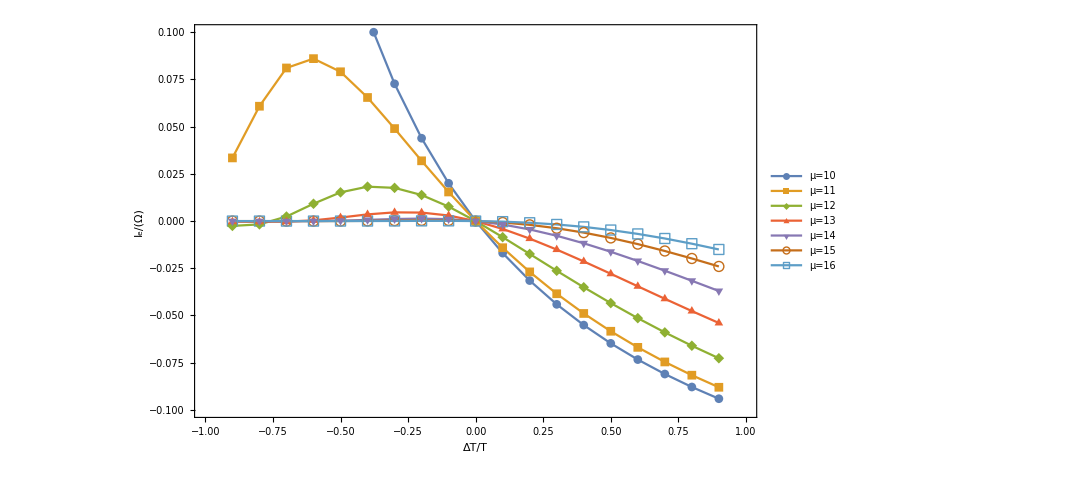

```mathematica
datas2=Import["op2.Je.json"];
(*Rescale unit*)
datas2⟦All,All,2⟧=datas2⟦All,All,2⟧/(2π);

ListLinePlot[datas2,PlotRange->{{-1.0,1.0},{-0.1,0.1}},
FrameLabel->{"ΔT/T","I_e/(Ω)"},
PlotLegends->Placed[{"μ=10","μ=11","μ=12","μ=13","μ=14","μ=15","μ=16"},{0.68,0.7}],
styles,
PlotMarkers->Automatic,Frame->True,ImageSize->800
]
```

## Operation 3: Electronic heating & cooling

Change Δμ=μ1-μ2, keep μ1+μ2=20 and the other parameters. The cooling effect only appear in a small bias window. This phenomena need to be concerned.

```mathematica
{
ℏ=1,Ω=1,k=1,T=1,Te=1,
γ1=0.5,γ2=0.5,
μ1=10,μ2=10,
ϵ1=10.5,ϵ2=9.5,t=0,
γph=0.5
};
μ=10;
ProgressIndicator[Dynamic[pr],{0.1,1.9}]
datas3=Table[pr=T;μ1=μ+Δμ/2;μ2=μ-Δμ/2;Te=T;{Δμ,J11+J12+J21+J22},{T,0.1,1.9,0.3},{Δμ,-10,10}];
Export["op3.J.json",datas3]
```

op3.J.json

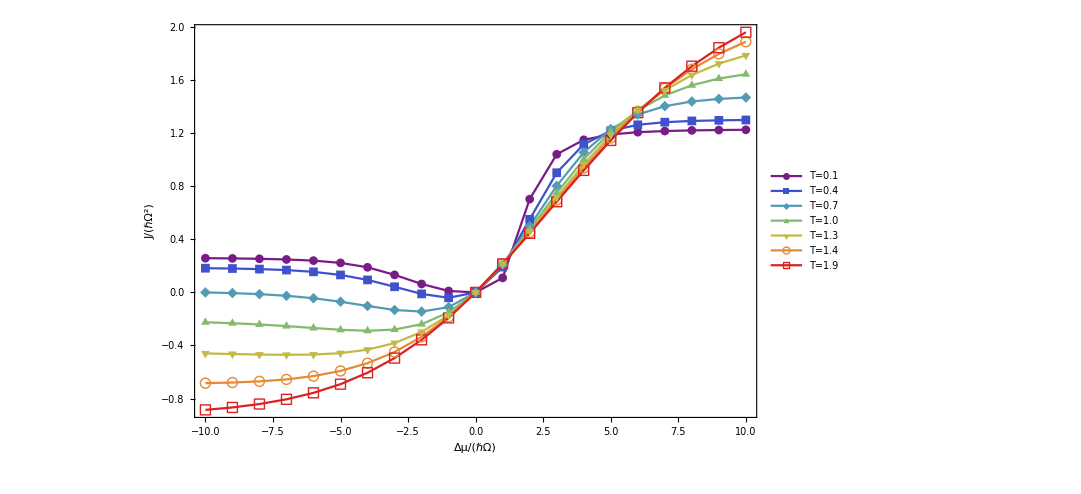

```mathematica
datas3=Import["op3.J.json"];
(*Rescale unit*)
datas3⟦All,All,2⟧=datas3⟦All,All,2⟧/(2π);

ListLinePlot[datas3,PlotRange->Automatic,
FrameLabel->{"Δμ/(ℏΩ)","J/(ℏΩ^2)"},
PlotStyle->"Rainbow",
PlotLegends->Placed[{"T=0.1","T=0.4","T=0.7","T=1.0","T=1.3","T=1.4","T=1.9"},{0.2,0.7}],
styles,
PlotMarkers->Automatic,Frame->True,ImageSize->800
]
```